## 1 step: R -> B -> P1

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5]
e1 = -k1*L1*r+kd1*b1+kd1*p1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1==0;(*P1*)
(**)
e4 = -k2*L2*r+kd2*b2+kd2*p2==0;
e5 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;
e6 = kp*b2-kdp*p2-kd2*p2==0;
(*P2*)
```

### Solutions

```mathematica
Clear[ex1]
solx=Solve[{e1,e2,e3,r+b1+p1==1},{r,b1,p1}][[1]];
r1 = ((p1)/.solx);
(**)
solx=Solve[{e4,e5,e6,r+b2+p2==1},{r,b2,p2}][[1]];
r2 = ((p2)/.solx);
ex1[δ_,ω_,ρ_]=FullSimplify[(r1/r2)/.{u1->u,u2->u}];
ex1[δ,ω,0]
(**)
```

(δ+ω+ρ ω)/(1+ω+ρ ω)

(δ+ω)/(1+ω)

## 2 steps: R -> B -> P1 -> P2

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5]
e1 =-k1*L1*r+kd1*b1+kd1*p1+kd1*q1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1==0;(*P1*)
(**)
e5 =-k2*L2*r+kd2*b2+kd2*p2+kd2*q2==0;(*R*)
e6 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e7 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2==0;(*P1*)
e8 = kp*p2-kdp*q2-kd2*q2==0;(*P1*)
(**)
(*P2*)
```

### Solutions

```mathematica
solx=Solve[{e1,e2,e3,e4,r+b1+p1+q1==1},{r,b1,p1,q1}][[1]];
r1 = ((q1)/.solx);
(**)
solx=Solve[{e5,e6,e7,e8,r+b2+p2+q2==1},{r,b2,p2,q2}][[1]];
r2 = ((q2)/.solx);
ex2[δ_,ω_,ρ_]=FullSimplify[(r1/r2)/.{u1->u,u2->u},Assumptions->{δ>0,ω>0,ρ>0}];
FullSimplify[ex2[δ,ω,0]]
```

(δ^2+2 δ (1+ρ) ω+(1+ρ+ρ^2) ω^2)/(1+ω (2+ω+ρ (2+ω+ρ ω)))

(δ+ω)^2/(1+ω)^2

## 3 steps: R -> B -> P1 -> P2 -> P3

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10]
e1 =-k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1==0;(*P1*)
e5 = kp*q1-kdp*f1-kd1*f1==0;
(**)
e6 =-k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2==0;(*R*)
e7 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e8 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2==0;(*P1*)
e9 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2==0;(*P1*)
e10 = kp*q2-kdp*f2-kd2*f2==0;
(**)
```

### Solutions

```mathematica
solx=Solve[{e1,e2,e3,e4,e5,r+b1+p1+q1+f1==1},{r,b1,p1,q1,f1}][[1]];
r1 = ((f1)/.solx);
(**)
solx=Solve[{e6,e7,e8,e9,e10,r+b2+p2+q2+f2==1},{r,b2,p2,q2,f2}][[1]];
r2 = ((f2)/.solx);
ex3[δ_,ω_,ρ_]=FullSimplify[(r1/r2)/.{u1->u,u2->u}];
FullSimplify[ex3[δ,ω,0]]
```

(δ+ω)^3/(1+ω)^3

## 4 steps: R -> B -> P1 -> P2 -> P3 -> P4

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10]
e1 =-k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1+kd1*g1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1==0;(*P1*)
e5 = kp*q1-kdp*f1-kd1*f1-kp*f1+kdp*g1==0;
e6 = kp*f1-kdp*g1-kd1*g1==0;
(**)
e7 =-k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2+kd2*g2==0;(*R*)
e8 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e9 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2==0;(*P1*)
e10 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2==0;(*P1*)
e11 = kp*q2-kdp*f2-kd2*f2-kp*f2+kdp*g2==0;
e12 = kp*f2-kdp*g2-kd2*g2==0;
(**)
```

### Solutions

```mathematica
solx=Solve[{e1,e2,e3,e4,e5,e6,r+b1+p1+q1+f1+g1==1},{r,b1,p1,q1,f1,g1}][[1]];
r1 = ((g1)/.solx);
(**)
solx=Solve[{e7,e8,e9,e10,e11,e12,r+b2+p2+q2+f2+g2==1},{r,b2,p2,q2,f2,g2}][[1]];
r2 = ((g2)/.solx);
ex4[δ_,ω_,ρ_]=FullSimplify[(r1/r2)/.{u1->u,u2->u}];
FullSimplify[ex4[δ,ω,0]]
```

(δ+ω)^4/(1+ω)^4

### Concentrations profiles

```mathematica
solx1=Solve[{e1,e2,e3,e4,e5,e6,r+b1+p1+q1+f1+g1==1},{r,b1,p1,q1,f1,g1}][[1]];
solx2=Solve[{e7,e8,e9,e10,e11,e12,r+b2+p2+q2+f2+g2==1},{r,b2,p2,q2,f2,g2}][[1]];
FullSimplify[Limit[({p1,q1,f1,g1}/.solx1),u1->Infinity]/.{ρ->0}]
FullSimplify[Limit[({p2,q2,f2,g2}/.solx2),u2->Infinity]/.{ρ->0}]
```

{ω/(1+ω)^2,ω^2/(1+ω)^3,ω^3/(1+ω)^4,ω^4/(1+ω)^4}

{(δ ω)/(δ+ω)^2,(δ ω^2)/(δ+ω)^3,(δ ω^3)/(δ+ω)^4,ω^4/(δ+ω)^4}

## 5 steps

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10]
e1 =-k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1+kd1*g1+kd1*h1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1==0;(*P1*)
e5 = kp*q1-kdp*f1-kd1*f1-kp*f1+kdp*g1==0;
e6 = kp*f1-kdp*g1-kd1*g1-kp*g1+kdp*h1==0;
e7 = kp*g1-kdp*h1-kd1*h1==0;
(**)
e8 =-k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2+kd2*g2+kd2*h2==0;(*R*)
e9 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e10 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2==0;(*P1*)
e11 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2==0;(*P1*)
e12 = kp*q2-kdp*f2-kd2*f2-kp*f2+kdp*g2==0;
e13 = kp*f2-kdp*g2-kd2*g2-kp*g2+kdp*h2==0;
e14 = kp*g2-kdp*h2-kd2*h2==0;
(**)
```

### Solutions

```mathematica
solx=Solve[{e1,e2,e3,e4,e5,e6,e7,r+b1+p1+q1+f1+g1+h1==1},{r,b1,p1,q1,f1,g1,h1}][[1]];
r1 = ((h1)/.solx);
(**)
solx=Solve[{e8,e9,e10,e11,e12,e13,e14,r+b2+p2+q2+f2+g2+h2==1},{r,b2,p2,q2,f2,g2,h2}][[1]];
r2 = ((h2)/.solx);
ex5[δ_,ω_,ρ_]=FullSimplify[(r1/r2)/.{u1->u,u2->u}];
FullSimplify[ex5[δ,ω,0]]
```

(δ+ω)^5/(1+ω)^5

### Concentration profiles

```mathematica
solx1=Solve[{e1,e2,e3,e4,e5,e6,e7,r+b1+p1+q1+f1+g1+h1==1},{r,b1,p1,q1,f1,g1,h1}][[1]];
solx2=Solve[{e8,e9,e10,e11,e12,e13,e14,r+b2+p2+q2+f2+g2+h2==1},{r,b2,p2,q2,f2,g2,h2}][[1]];
FullSimplify[Limit[({p1,q1,f1,g1,h1}/.solx1),u1->Infinity]/.{ρ->0}]
```

{ω/(1+ω)^2,ω^2/(1+ω)^3,ω^3/(1+ω)^4,ω^4/(1+ω)^5,ω^5/(1+ω)^5}

## N-train concentrations

20.

δ ω^n (δ+ω)^(-1-n)

ω^n (δ+ω)^-n

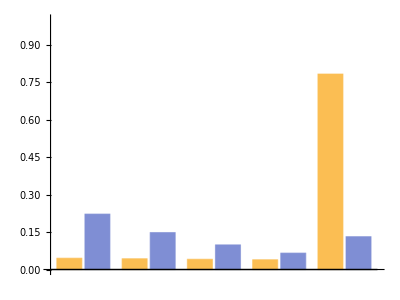

```mathematica
unbind = 0.05;
phosph = 1;
δE       = 10;
ωE = phosph/unbind
pn[δ_,ω_,n_]=δ*ω^n/(δ+ω)^(n+1)
pN[δ_,ω_,n_]=ω^n/(δ+ω)^n
nE = 5;
slowTrain=Append[Table[{n,pn[1.0,ωE,n]},{n,1,nE-1}],{nE,pN[1.0,ωE,nE]}];
fastTrain=Append[Table[{n+0.25,pn[δE,ωE,n]},{n,1,nE-1}],{nE+0.25,pN[δE,ωE,nE]}];
tbl = Table[{slowTrain[[i]][[2]],fastTrain[[i]][[2]]},{i,1,Length[slowTrain]}];
ListPlot[{slowTrain,fastTrain},PlotRange->{0.0,1}];
FullSimplify[pN[δ,ω,n]/pn[1,ω,n]];
FullSimplify[Sum[pn[δ,ω,n],{n,1,Ne-1}]+pN[δ,ω,Ne]];
Show[BarChart[tbl,AspectRatio->0.75],TextStyle->FontSize->20,PlotRange->{0,1}]
```